```mathematica
Exit[]
```

# Singlet sector nf^3parts

Main reference: 1610.07477,  we follow Eq. 3.10, 3.12, 3.13, 3.14

```mathematica
<<"/Users/giacomomagni/Documents/Wolfram Mathematica/Sigma.m"
<<"/Users/giacomomagni/Documents/Wolfram Mathematica/HarmonicSums.m"
```

Sigma - A summation package by Carsten Schneider — © RISC —  V 2.86 (June 15, 2021)  Help

HarmonicSums by Jakob Ablinger — © RISC — Version 1.0(30/03/21)Help

```mathematica
here = NotebookDirectory[];
Get[StringJoin[here, "constants.m"]]
```

```mathematica
(* Singlet, large nf exact parts *)
Get[StringJoin[here, "singlet_nf3.m"]]
Get[StringJoin[here, "ns_nf3_nf2.m"]]
(* Singlet, asymptotic N-> Infinity, large nc limit *)
Get[StringJoin[here, "qcd_cusp.m"]]
Get[StringJoin[here, "gamma_thr.m"]]
(* Singlet, moments *)
Get[StringJoin[here, "gqq3nsp.m"]]
Get[StringJoin[here, "gqq3ps.m"]]
Get[StringJoin[here, "gqg3.m"]]
Get[StringJoin[here, "ggq3.m"]]
Get[StringJoin[here, "ggg3.m"]]
```

### Plotting routines

```mathematica
PlotNvalsSinglet[moments_, fexa_, nfpart_]:=Module[{Nmin, nvals,title},
	Nmin=2;
	nvals = Range[Nmin, 2 Length[moments],2];
	title = StringForm["relative diff N moment-fexa, Part prop to nf^``.", nfpart];
	ListPlot[
		MapThread[{#1, (#2 - fexa)/fexa //. QCDConstantsRules /. ZetaRules /. n -> #1} &, {nvals, Coefficient[moments,nf,nfpart]}], 
		PlotLabel->title
	]
];
```

### Nf^3 checks

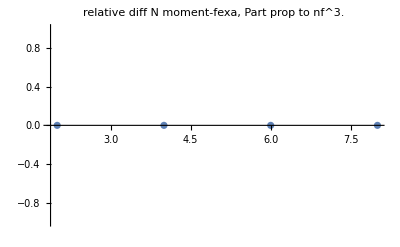

-Graphics-

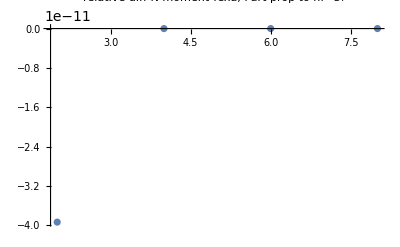

-Graphics-

```mathematica
(* check agreement  *)
(* qq ps *)
momentlist = {gqq3psN2, gqq3psN4, gqq3psN6, gqq3psN8};
PlotNvalsSinglet[momentlist, gqq3psnf3, 3]
(* qg *)
momentlist = {gqg3N2, gqg3N4, gqg3N6, gqg3N8};
PlotNvalsSinglet[momentlist, gqg3nf3,3]
(* gq *)
momentlist = {ggq3N2, ggq3N4, ggq3N6, ggq3N8};
PlotNvalsSinglet[momentlist, ggq3nf3, 3]
(* gg *)
momentlist = {ggg3N2, ggg3N4, ggg3N6, ggg3N8};
PlotNvalsSinglet[momentlist, ggg3nf3, 3]
```

### Nf^3 simplify

```mathematica
SimplifyNf3[f_] := f //. QCDConstantsRules /. ZetaRules //. harmonics234
```

```mathematica
(* qq ps *)
SimplifyNf3[gqq3psnf3] // N
```

1.33333 (16.3058/(-1.+n)+3.55556/n^5-17.1852/n^4+28.8395/n^3-48.9525/n^2+23.0935/n+39.1111/(1.+n)^5-61.037/(1.+n)^4-10.6667/(1.+n)^3+59.2944/(1.+n)^2-94.2047/(1.+n)+18.963/(2.+n)^4-34.7654/(2.+n)^3+14.2222/(2.+n)^2+54.8053/(2.+n)-(1.58025 S[1.,n])/(-1.+n)+(7.11111 S[1.,n])/n^4-(34.3704 S[1.,n])/n^3+(38.716 S[1.,n])/n^2-(37.1358 S[1.,n])/n+(35.5556 S[1.,n])/(1.+n)^4-(43.8519 S[1.,n])/(1.+n)^3-(39.5062 S[1.,n])/(1.+n)^2+(89.284 S[1.,n])/(1.+n)+(18.963 S[1.,n])/(2.+n)^3-(34.7654 S[1.,n])/(2.+n)^2-(50.5679 S[1.,n])/(2.+n)+(4.74074 (S[1.,n]^2+S[2.,n]))/(-1.+n)+(7.11111 (S[1.,n]^2+S[2.,n]))/n^3-(15.4074 (S[1.,n]^2+S[2.,n]))/n^2+(13.037 (S[1.,n]^2+S[2.,n]))/n+(14.2222 (S[1.,n]^2+S[2.,n]))/(1.+n)^3-(4.74074 (S[1.,n]^2+S[2.,n]))/(1.+n)^2-(20.1481 (S[1.,n]^2+S[2.,n]))/(1.+n)+(9.48148 (S[1.,n]^2+S[2.,n]))/(2.+n)^2+(2.37037 (S[1.,n]^2+S[2.,n]))/(2.+n)-(1.58025 (S[1.,n]^3+3. S[1.,n] S[2.,n]+2. S[3.,n]))/(-1.+n)+(2.37037 (S[1.,n]^3+3. S[1.,n] S[2.,n]+2. S[3.,n]))/n^2-(1.18519 (S[1.,n]^3+3. S[1.,n] S[2.,n]+2. S[3.,n]))/n+(2.37037 (S[1.,n]^3+3. S[1.,n] S[2.,n]+2. S[3.,n]))/(1.+n)^2+(1.18519 (S[1.,n]^3+3. S[1.,n] S[2.,n]+2. S[3.,n]))/(1.+n)+(1.58025 (S[1.,n]^3+3. S[1.,n] S[2.,n]+2. S[3.,n]))/(2.+n))

```mathematica
(* qg *)
SimplifyNf3[gqg3nf3] //N
```

1.33333 (44.5669/(-1.+n)-82.3704/n^5+95.3086/n^4-298.695/n^3+334.452/n^2-576.164/n-156.444/(1.+n)^6+271.407/(1.+n)^5-142.617/(1.+n)^4+49.2093/(1.+n)^3+242.316/(1.+n)^2+383.955/(1.+n)+75.8519/(2.+n)^5-18.963/(2.+n)^4-28.9712/(2.+n)^3+57.9044/(2.+n)^2+153.56/(2.+n)-(3.16049 S21)/(-1.+n)+(7.11111 S21)/n^3-(10.6667 S21)/n^2+(32. S21)/n-(14.2222 S21)/(1.+n)^3-(53.3333 S21)/(1.+n)+(9.48148 S21)/(2.+n)^2+(24.4938 S21)/(2.+n)-(7.72565 S[1.,n])/(-1.+n)+(35.5556 S[1.,n])/n^5-(53.3333 S[1.,n])/n^4+(149.728 S[1.,n])/n^3-(189.498 S[1.,n])/n^2+(219.774 S[1.,n])/n-(71.1111 S[1.,n])/(1.+n)^5+(75.8519 S[1.,n])/(1.+n)^4+(45.4321 S[1.,n])/(1.+n)^3-(24.6914 S[1.,n])/(1.+n)^2-(242.018 S[1.,n])/(1.+n)+(37.9259 S[1.,n])/(2.+n)^4+(53.7284 S[1.,n])/(2.+n)^3+(39.7695 S[1.,n])/(2.+n)^2+(33.8421 S[1.,n])/(2.+n)-(8.95473 S[2.,n])/(-1.+n)+(28.4444 S[2.,n])/n^4-(47.4074 S[2.,n])/n^3+(117.333 S[2.,n])/n^2-(128.527 S[2.,n])/n-(71.1111 S[2.,n])/(1.+n)^4+(9.48148 S[2.,n])/(1.+n)^3+(60.4444 S[2.,n])/(1.+n)^2-(11.5885 S[2.,n])/(1.+n)+(56.8889 S[2.,n])/(2.+n)^3+(112.198 S[2.,n])/(2.+n)^2+(144.988 S[2.,n])/(2.+n)-(2.37037 (S[1.,n]^2+S[2.,n]))/(-1.+n)+(2.37037 (S[1.,n]^2+S[2.,n]))/n^3+(3.35802 (S[1.,n]^2+S[2.,n]))/n^2-(13.6955 (S[1.,n]^2+S[2.,n]))/n+(7.11111 (S[1.,n]^2+S[2.,n]))/(1.+n)^4+(9.48148 (S[1.,n]^2+S[2.,n]))/(1.+n)^3-(2.96296 (S[1.,n]^2+S[2.,n]))/(1.+n)^2+(53.7613 (S[1.,n]^2+S[2.,n]))/(1.+n)-(9.48148 (S[1.,n]^2+S[2.,n]))/(2.+n)^3-(21.3333 (S[1.,n]^2+S[2.,n]))/(2.+n)^2-(38.6502 (S[1.,n]^2+S[2.,n]))/(2.+n)-(3.16049 S[3.,n])/(-1.+n)+(7.11111 S[3.,n])/n^3-(10.6667 S[3.,n])/n^2+(28.0494 S[3.,n])/n-(14.2222 S[3.,n])/(1.+n)^3-(43.0617 S[3.,n])/(1.+n)+(9.48148 S[3.,n])/(2.+n)^2+(14.2222 S[3.,n])/(2.+n)-(3.16049 (-1. S21+S[1.,n] S[2.,n]+S[3.,n]))/(-1.+n)+(7.11111 (-1. S21+S[1.,n] S[2.,n]+S[3.,n]))/n^3-(10.6667 (-1. S21+S[1.,n] S[2.,n]+S[3.,n]))/n^2+(32. (-1. S21+S[1.,n] S[2.,n]+S[3.,n]))/n-(14.2222 (-1. S21+S[1.,n] S[2.,n]+S[3.,n]))/(1.+n)^3-(53.3333 (-1. S21+S[1.,n] S[2.,n]+S[3.,n]))/(1.+n)+(9.48148 (-1. S21+S[1.,n] S[2.,n]+S[3.,n]))/(2.+n)^2+(24.4938 (-1. S21+S[1.,n] S[2.,n]+S[3.,n]))/(2.+n)+(0.526749 (S[1.,n]^3+3. S[1.,n] S[2.,n]+2. S[3.,n]))/(-1.+n)-(1.18519 (S[1.,n]^3+3. S[1.,n] S[2.,n]+2. S[3.,n]))/n^3+(1.97531 (S[1.,n]^3+3. S[1.,n] S[2.,n]+2. S[3.,n]))/n^2-(4.6749 (S[1.,n]^3+3. S[1.,n] S[2.,n]+2. S[3.,n]))/n+(2.37037 (S[1.,n]^3+3. S[1.,n] S[2.,n]+2. S[3.,n]))/(1.+n)^3+(7.57202 (S[1.,n]^3+3. S[1.,n] S[2.,n]+2. S[3.,n]))/(1.+n)-(1.58025 (S[1.,n]^3+3. S[1.,n] S[2.,n]+2. S[3.,n]))/(2.+n)^2-(2.76543 (S[1.,n]^3+3. S[1.,n] S[2.,n]+2. S[3.,n]))/(2.+n)-(1.18519 (0.0416667 S[1.,n]^4+0.25 S[1.,n]^2 S[2.,n]+0.125 S[2.,n]^2+0.333333 S[1.,n] S[3.,n]+0.25 S[4.,n]))/n+(2.37037 (0.0416667 S[1.,n]^4+0.25 S[1.,n]^2 S[2.,n]+0.125 S[2.,n]^2+0.333333 S[1.,n] S[3.,n]+0.25 S[4.,n]))/(1.+n)-(2.37037 (0.0416667 S[1.,n]^4+0.25 S[1.,n]^2 S[2.,n]+0.125 S[2.,n]^2+0.333333 S[1.,n] S[3.,n]+0.25 S[4.,n]))/(2.+n)+(3.55556 S[4.,n])/n-(7.11111 S[4.,n])/(1.+n)+(7.11111 S[4.,n])/(2.+n))+3. (2.53815/(-1.+n)+3.55556/n^5+5.7284/n^4+4.55967/n^3+2.0364/n^2-1.11697/n+26.0741/(1.+n)^5-56.0988/(1.+n)^4+70.0247/(1.+n)^3-56.5856/(1.+n)^2+23.2688/(1.+n)+18.963/(2.+n)^5-37.9259/(2.+n)^4+22.3868/(2.+n)^3+25.9/(2.+n)^2-33.7105/(2.+n)-(3.95062 S21)/n-(2.37037 S21)/(1.+n)^2+(7.90123 S21)/(1.+n)+(2.37037 S21)/(2.+n)^2-(7.90123 S21)/(2.+n)+(1.18519 S211)/n-(2.37037 S211)/(1.+n)+(2.37037 S211)/(2.+n)+(1.18519 S31)/n-(2.37037 S31)/(1.+n)+(2.37037 S31)/(2.+n)+(4.74074 S[-4.,n])/n-(9.48148 S[-4.,n])/(1.+n)+(9.48148 S[-4.,n])/(2.+n)-(7.90123 S[-3.,n])/n+(11.0617 S[-3.,n])/(1.+n)-(11.0617 S[-3.,n])/(2.+n)+(2.50206 S[-2.,n])/n+(0.592593 S[-2.,n])/(1.+n)^2-(0.658436 S[-2.,n])/(1.+n)+(1.84362 S[-2.,n])/(2.+n)+(0.351166 S[1.,n])/(-1.+n)-(9.48148 S[1.,n])/n^4+(8.93827 S[1.,n])/n^3-(17.4321 S[1.,n])/n^2+(15.0158 S[1.,n])/n+(14.2222 S[1.,n])/(1.+n)^4-(1.77778 S[1.,n])/(1.+n)^3-(14.535 S[1.,n])/(1.+n)^2+(48.2893 S[1.,n])/(1.+n)+(9.48148 S[1.,n])/(2.+n)^4-(46.6173 S[1.,n])/(2.+n)^3-(42.2716 S[1.,n])/(2.+n)^2-(64.9615 S[1.,n])/(2.+n)+(1.71193 S[2.,n])/(-1.+n)-(2.37037 S[2.,n])/n^3+(0.740741 S[2.,n])/n^2-(7.7037 S[2.,n])/n+(9.48148 S[2.,n])/(1.+n)^3-(15.0123 S[2.,n])/(1.+n)^2+(27.3086 S[2.,n])/(1.+n)-(4.74074 S[2.,n])/(2.+n)^3+(2.76543 S[2.,n])/(2.+n)^2-(21.0206 S[2.,n])/(2.+n)+(0.855967 (S[1.,n]^2+S[2.,n]))/(-1.+n)-(1.18519 (S[1.,n]^2+S[2.,n]))/n^3+(0.37037 (S[1.,n]^2+S[2.,n]))/n^2-(2.60082 (S[1.,n]^2+S[2.,n]))/n+(2.91358 (S[1.,n]^2+S[2.,n]))/(1.+n)^2+(5.27572 (S[1.,n]^2+S[2.,n]))/(1.+n)+(2.37037 (S[1.,n]^2+S[2.,n]))/(2.+n)^3-(6.51852 (S[1.,n]^2+S[2.,n]))/(2.+n)^2-(2.87243 (S[1.,n]^2+S[2.,n]))/(2.+n)-(3.95062 S[3.,n])/n+(2.37037 S[3.,n])/(1.+n)^2+(3.16049 S[3.,n])/(1.+n)-(2.37037 S[3.,n])/(2.+n)^2-(3.16049 S[3.,n])/(2.+n)+(3.95062 (-1. S21+S[1.,n] S[2.,n]+S[3.,n]))/n+(2.37037 (-1. S21+S[1.,n] S[2.,n]+S[3.,n]))/(1.+n)^2-(7.90123 (-1. S21+S[1.,n] S[2.,n]+S[3.,n]))/(1.+n)-(2.37037 (-1. S21+S[1.,n] S[2.,n]+S[3.,n]))/(2.+n)^2+(7.90123 (-1. S21+S[1.,n] S[2.,n]+S[3.,n]))/(2.+n)-(0.658436 (S[1.,n]^3+3. S[1.,n] S[2.,n]+2. S[3.,n]))/n-(0.395062 (S[1.,n]^3+3. S[1.,n] S[2.,n]+2. S[3.,n]))/(1.+n)^2+(1.31687 (S[1.,n]^3+3. S[1.,n] S[2.,n]+2. S[3.,n]))/(1.+n)+(0.395062 (S[1.,n]^3+3. S[1.,n] S[2.,n]+2. S[3.,n]))/(2.+n)^2-(1.31687 (S[1.,n]^3+3. S[1.,n] S[2.,n]+2. S[3.,n]))/(2.+n)+(1.18519 (0.0416667 S[1.,n]^4+0.25 S[1.,n]^2 S[2.,n]+0.125 S[2.,n]^2+0.333333 S[1.,n] S[3.,n]+0.25 S[4.,n]))/n-(2.37037 (0.0416667 S[1.,n]^4+0.25 S[1.,n]^2 S[2.,n]+0.125 S[2.,n]^2+0.333333 S[1.,n] S[3.,n]+0.25 S[4.,n]))/(1.+n)+(2.37037 (0.0416667 S[1.,n]^4+0.25 S[1.,n]^2 S[2.,n]+0.125 S[2.,n]^2+0.333333 S[1.,n] S[3.,n]+0.25 S[4.,n]))/(2.+n)+(3.55556 S[4.,n])/n-(7.11111 S[4.,n])/(1.+n)+(7.11111 S[4.,n])/(2.+n)-(0.592593 (S[2.,n]^2+S[4.,n]))/n+(1.18519 (S[2.,n]^2+S[4.,n]))/(1.+n)-(1.18519 (S[2.,n]^2+S[4.,n]))/(2.+n)-(1.18519 (-1. S31+S[1.,n] S[3.,n]+S[4.,n]))/n+(2.37037 (-1. S31+S[1.,n] S[3.,n]+S[4.,n]))/(1.+n)-(2.37037 (-1. S31+S[1.,n] S[3.,n]+S[4.,n]))/(2.+n)+(1.18519 (-2.+S31+S21 S[1.,n]+0.5 (S[2.,n]^2+S[4.,n])))/n-(2.37037 (-2.+S31+S21 S[1.,n]+0.5 (S[2.,n]^2+S[4.,n])))/(1.+n)+(2.37037 (-2.+S31+S21 S[1.,n]+0.5 (S[2.,n]^2+S[4.,n])))/(2.+n)-(1.18519 (S211+0.5 (-2. S31+S[1.,n] S[3.,n]+S[1.,n] (-2. S21+S[1.,n] S[2.,n]+S[3.,n])+S[4.,n])))/n+(2.37037 (S211+0.5 (-2. S31+S[1.,n] S[3.,n]+S[1.,n] (-2. S21+S[1.,n] S[2.,n]+S[3.,n])+S[4.,n])))/(1.+n)-(2.37037 (S211+0.5 (-2. S31+S[1.,n] S[3.,n]+S[1.,n] (-2. S21+S[1.,n] S[2.,n]+S[3.,n])+S[4.,n])))/(2.+n))

```mathematica
(* gq *)
SimplifyNf3[ggq3nf3] //N
```

1.33333 (-11.3973/(-1.+n)+11.3973/n-2.37037/(1.+n)^4+6.32099/(1.+n)^3-3.16049/(1.+n)^2-5.69864/(1.+n)-(6.32099 S[1.,n])/(-1.+n)+(6.32099 S[1.,n])/n-(2.37037 S[1.,n])/(1.+n)^3+(6.32099 S[1.,n])/(1.+n)^2-(3.16049 S[1.,n])/(1.+n)+(6.32099 (S[1.,n]^2+S[2.,n]))/(-1.+n)-(6.32099 (S[1.,n]^2+S[2.,n]))/n-(1.18519 (S[1.,n]^2+S[2.,n]))/(1.+n)^2+(3.16049 (S[1.,n]^2+S[2.,n]))/(1.+n)-(0.790123 (S[1.,n]^3+3. S[1.,n] S[2.,n]+2. S[3.,n]))/(-1.+n)+(0.790123 (S[1.,n]^3+3. S[1.,n] S[2.,n]+2. S[3.,n]))/n-(0.395062 (S[1.,n]^3+3. S[1.,n] S[2.,n]+2. S[3.,n]))/(1.+n))

```mathematica
(* gg *)
SimplifyNf3[ggg3nf3] // N
```

3. (-0.0205761+2.59924/(-1.+n)-1.18519/n^4-3.75309/n^3-5.67901/n^2-2.805/n-1.18519/(1.+n)^4+3.75309/(1.+n)^3-5.67901/(1.+n)^2+2.805/(1.+n)-2.59924/(2.+n)+2.45426 S[1.,n]-(8.6749 S[1.,n])/(-1.+n)+(2.37037 S[1.,n])/n^3+(7.50617 S[1.,n])/n^2+(7.90123 S[1.,n])/n-(2.37037 S[1.,n])/(1.+n)^3+(7.50617 S[1.,n])/(1.+n)^2-(7.90123 S[1.,n])/(1.+n)+(8.6749 S[1.,n])/(2.+n)-(2.5679 S[2.,n])/(-1.+n)+(2.37037 S[2.,n])/n^2+(1.62963 S[2.,n])/n+(2.37037 S[2.,n])/(1.+n)^2-(1.62963 S[2.,n])/(1.+n)+(2.5679 S[2.,n])/(2.+n)+(2.5679 (S[1.,n]^2+S[2.,n]))/(-1.+n)-(2.37037 (S[1.,n]^2+S[2.,n]))/n^2-(1.62963 (S[1.,n]^2+S[2.,n]))/n-(2.37037 (S[1.,n]^2+S[2.,n]))/(1.+n)^2+(1.62963 (S[1.,n]^2+S[2.,n]))/(1.+n)-(2.5679 (S[1.,n]^2+S[2.,n]))/(2.+n))+1.33333 (-0.633745-54.2317/(-1.+n)+3.55556/n^5+13.6296/n^4+27.6543/n^3+61.0019/n^2+26.2892/n+10.6667/(1.+n)^5-31.4074/(1.+n)^4+31.6049/(1.+n)^3-12.4796/(1.+n)^2+44.8219/(1.+n)-16.8794/(2.+n)-(9.48148 S21)/(-1.+n)+(14.2222 S21)/n^2+(21.3333 S21)/n+(14.2222 S21)/(1.+n)^2-(21.3333 S21)/(1.+n)-(28.4444 S21)/(n (1.+n))+(9.48148 S21)/(2.+n)+(48.7243 S[1.,n])/(-1.+n)-(7.11111 S[1.,n])/n^4-(27.2593 S[1.,n])/n^3-(36.3457 S[1.,n])/n^2-(56.4938 S[1.,n])/n+(7.11111 S[1.,n])/(1.+n)^4-(17.7778 S[1.,n])/(1.+n)^3+(3.95062 S[1.,n])/(1.+n)^2+(4.34568 S[1.,n])/(1.+n)+(3.42387 S[1.,n])/(2.+n)+(27.6543 S[2.,n])/(-1.+n)-(7.11111 S[2.,n])/n^3-(27.2593 S[2.,n])/n^2-(16.5926 S[2.,n])/n+(7.11111 S[2.,n])/(1.+n)^3-(27.2593 S[2.,n])/(1.+n)^2+(16.5926 S[2.,n])/(1.+n)-(27.6543 S[2.,n])/(2.+n)-(15.0123 (S[1.,n]^2+S[2.,n]))/(-1.+n)+(7.11111 (S[1.,n]^2+S[2.,n]))/n^3+(8.2963 (S[1.,n]^2+S[2.,n]))/n^2+(22.5185 (S[1.,n]^2+S[2.,n]))/n+(4.74074 (S[1.,n]^2+S[2.,n]))/(1.+n)^2-(15.4074 (S[1.,n]^2+S[2.,n]))/(1.+n)+(7.90123 (S[1.,n]^2+S[2.,n]))/(2.+n)+(4.74074 S[3.,n])/(-1.+n)-(7.11111 S[3.,n])/n^2-(10.6667 S[3.,n])/n-(7.11111 S[3.,n])/(1.+n)^2+(10.6667 S[3.,n])/(1.+n)+(14.2222 S[3.,n])/(n (1.+n))-(4.74074 S[3.,n])/(2.+n)-(9.48148 (-1. S21+S[1.,n] S[2.,n]+S[3.,n]))/(-1.+n)+(14.2222 (-1. S21+S[1.,n] S[2.,n]+S[3.,n]))/n^2+(21.3333 (-1. S21+S[1.,n] S[2.,n]+S[3.,n]))/n+(14.2222 (-1. S21+S[1.,n] S[2.,n]+S[3.,n]))/(1.+n)^2-(21.3333 (-1. S21+S[1.,n] S[2.,n]+S[3.,n]))/(1.+n)-(28.4444 (-1. S21+S[1.,n] S[2.,n]+S[3.,n]))/(n (1.+n))+(9.48148 (-1. S21+S[1.,n] S[2.,n]+S[3.,n]))/(2.+n)+(1.58025 (S[1.,n]^3+3. S[1.,n] S[2.,n]+2. S[3.,n]))/(-1.+n)-(2.37037 (S[1.,n]^3+3. S[1.,n] S[2.,n]+2. S[3.,n]))/n^2-(3.55556 (S[1.,n]^3+3. S[1.,n] S[2.,n]+2. S[3.,n]))/n-(2.37037 (S[1.,n]^3+3. S[1.,n] S[2.,n]+2. S[3.,n]))/(1.+n)^2+(3.55556 (S[1.,n]^3+3. S[1.,n] S[2.,n]+2. S[3.,n]))/(1.+n)+(4.74074 (S[1.,n]^3+3. S[1.,n] S[2.,n]+2. S[3.,n]))/(n (1.+n))-(1.58025 (S[1.,n]^3+3. S[1.,n] S[2.,n]+2. S[3.,n]))/(2.+n))

### Export to .C

```mathematica
exportMe[expr_, fp_] := Module[{me, out},
       me = SimplifyNf3[expr] /. harmonics /. harmonicminus // N;
       Print["writing to ", fp];
       out = OpenWrite[fp];
       WriteString[out, ToString@CForm@me];
       Close[out];
   ];
here = NotebookDirectory[];
nf3singletpath = StringJoin[here, "singlet_nf3/"];
exportMe[ggg3nf3, StringJoin[nf3singletpath, "ggg3nf3.c"]];
exportMe[ggq3nf3, StringJoin[nf3singletpath, "ggq3nf3.c"]];
exportMe[gqg3nf3, StringJoin[nf3singletpath, "gqg3nf3.c"]];
exportMe[gqq3psnf3, StringJoin[nf3singletpath, "gqq3psnf3.c"]];
```

writing to /Users/giacomomagni/Documents/Wolfram Mathematica/Ad_N3LO/singlet_nf3/ggg3nf3.c

writing to /Users/giacomomagni/Documents/Wolfram Mathematica/Ad_N3LO/singlet_nf3/ggq3nf3.c

writing to /Users/giacomomagni/Documents/Wolfram Mathematica/Ad_N3LO/singlet_nf3/gqg3nf3.c

writing to /Users/giacomomagni/Documents/Wolfram Mathematica/Ad_N3LO/singlet_nf3/gqq3psnf3.c

### Test momentum conservation

```mathematica
gqg3nf3 + ggg3nf3 /. n -> 2 /. QCDConstantsRules /. ZetaRules // N
ggq3nf3 + gqq3psnf3 + gqq3nsnf3 /. n -> 2 /. QCDConstantsRules /. ZetaRules // N
```

0.

-8.88178×10^-16